```mathematica
(*Operacja tworzenia macierzy połączonej. "a" to główna macierz równania, "b" to wyrazy wolne. UWAGA wurazy wolne muszą być dodatkowo otoczone listą np zamiast {2 , k} należy stosować {{2 , k}}:*)
makeJoined[a_ , b_]:= Transpose[Join[Transpose[a] , b]];
(*Mnożenie wiersza "row" macierzy "joined" przez liczbę "num":*)
mulRow[row_ , num_][joined_]:=Join[joined[[1;;row-1]],{num joined[[row]]},joined[[row+1;;]]];
(*Dodawanie wiersza "from" macierzy "joined" do wiersza "to":*)
addRow[from_, to_][joined_]:=Join[joined[[1;;to-1]],{joined[[from]]+joined[[to]]},joined[[to+1;;]]];
(*Dodawanie wiersza "from" macierzy "joined", przemnożonego dodatkowo przez "mul", do wiersza "to":*)
addRow[from_ ,mul_, to_][joined_]:=Join[joined[[1;;to-1]],{mul joined[[from]]+joined[[to]]},joined[[to+1;;]]];
```

## Liczenie wyznacznika wprost z definicji, Leibnitz :

```mathematica
Clear[a , n , per , sgn , ele , val];
```

```mathematica
a = {{1 ,2 , 2} , {4 , 5 , 6} , {7 , 2 , 9} };
```

```mathematica
(*a = {{1 ,2 , 2 , 3} , {4 , 5 , 6 , 2} , {7 , 2 , 9 , 8} , {7 , 3 , 9 , 8}};*)
```

```mathematica
n = Dimensions[a][[1]];
```

```mathematica
per = Permutations[Range[n]]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
sgn = Signature/@per
```

{1,-1,-1,1,1,-1}

```mathematica
ele = Partition[Riffle[Range[n] , #] , 2]&/@per
```

{{{1,1},{2,2},{3,3}},{{1,1},{2,3},{3,2}},{{1,2},{2,1},{3,3}},{{1,2},{2,3},{3,1}},{{1,3},{2,1},{3,2}},{{1,3},{2,2},{3,1}}}

```mathematica
val = Table[Times@@(a[[#[[1]] , #[[2]]]]&/@ele[[ii]]) , {ii , 1 , Dimensions[ele][[1]]}]
```

{45,12,72,84,16,70}

```mathematica
val sgn
```

{45,-12,-72,84,16,-70}

```mathematica
Total[%]
```

-9

```mathematica
Det[a]
```

-9

## Rozwijanie wyznacznika:

```mathematica
rmRowCol[r_ , c_][m_]:=Transpose[Delete[Transpose[Delete[m , r]] , c]];
```

```mathematica
det[num_,{{x_}}]:=num x;
```

```mathematica
itDet[row_][det[num_ , m_]]:=Table[det[num m[[row , ii]](-1)^(row + ii) ,rmRowCol[row , ii][m] ] , {ii , 1, Dimensions[m][[2]]}];
```

```mathematica
itDet[row_][{d__det}]:= Flatten[itDet[row]/@{d}];
```

```mathematica
a = {{1 ,2 , 2 , 3} , {4 , 5 , 6 , 2} , {7 , 2 , 9 , 8} , {7 , 3 , 9 , 8}}
```

{{1,2,2,3},{4,5,6,2},{7,2,9,8},{7,3,9,8}}

```mathematica
det[1 , a]//TraditionalForm
```

det(1,(1 | 2 | 2 | 3
4 | 5 | 6 | 2
7 | 2 | 9 | 8
7 | 3 | 9 | 8))

```mathematica
itDet[1][%]//TraditionalForm
```

{det(1,(5 | 6 | 2
2 | 9 | 8
3 | 9 | 8)),det(-2,(4 | 6 | 2
7 | 9 | 8
7 | 9 | 8)),det(2,(4 | 5 | 2
7 | 2 | 8
7 | 3 | 8)),det(-3,(4 | 5 | 6
7 | 2 | 9
7 | 3 | 9))}

```mathematica
itDet[2][%]//TraditionalForm
```

{det(-2,(6 | 2
9 | 8)),det(9,(5 | 2
3 | 8)),det(-8,(5 | 6
3 | 9)),det(14,(6 | 2
9 | 8)),det(-18,(4 | 2
7 | 8)),det(16,(4 | 6
7 | 9)),det(-14,(5 | 2
3 | 8)),det(4,(4 | 2
7 | 8)),det(-16,(4 | 5
7 | 3)),det(21,(5 | 6
3 | 9)),det(-6,(4 | 6
7 | 9)),det(27,(4 | 5
7 | 3))}

```mathematica
itDet[1][%]//TraditionalForm
```

{-96,36,360,-54,-360,144,672,-252,-576,252,576,-672,-560,84,128,-56,-192,560,945,-378,-216,252,324,-945}

```mathematica
Total[%]
```

-24

```mathematica
Det[a]
```

-24

## Zabawa z transformacją kwadracika, jak to się ma do wyznacznika?

```mathematica
points = Flatten[Table[{x , y} , {x , 0 , 1 , 0.05} , {y , 0 , 1 , 0.05}] , 1];
```

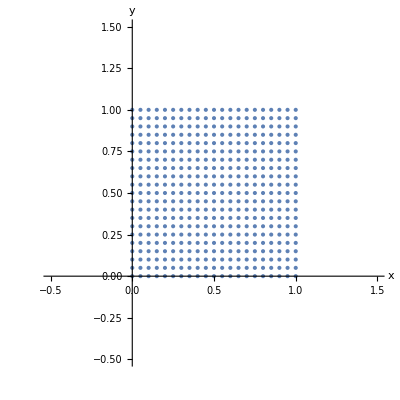

```mathematica
ListPlot[points , AspectRatio->1 , PlotRange->{{-0.5 , 1.5} , {-0.5 , 1.5}} , AxesLabel->{"x" , "y"}]
```

```mathematica
a = {{1 , 0} , {0 , 1}};
```

```mathematica
ListPlot[Function[r , a.r]/@points , AspectRatio->1 , PlotRange->{{-0.5 , 1.5} , {-0.5 , 1.5}} , AxesLabel->{"x" , "y"}]
```

-Graphics-

```mathematica
a = {{1 , 0.1} , {0.1 , 1}}
```

{{1,0.1},{0.1,1}}

```mathematica
Manipulate[Show[ ListPlot[points   , PlotStyle->Blue],ListPlot[Function[r , {{a11 , a12} , {a21 , a22}}.r]/@points  , PlotStyle->Red], AspectRatio->1 , PlotRange->{{-0.5 , 1.5} , {-0.5 , 1.5}} , AxesLabel->{"x" , "y"}] , {{a11 , 1} , 0.5 , 1.5} , {{a12 , 0} , -0.5 , 0.5} , {{a21 , 0} , -0.5 , 0.5} , {{a22 , 1} , 0.5 , 1.5}]
```